## kompeticio

```mathematica
egyenletek={p1(1-1.5p2),p2(1-1.5p1)}
```

{p1 (1-1.5 p2),(1-1.5 p1) p2}

```mathematica
Egyensúly=Solve[egyenletek=={0,0}]
```

{{p1→0.,p2→0.},{p1→0.666667,p2→0.666667}}

```mathematica
s=Solve[p1(1-1.5p2)==0]
```

{{p1→0.},{p2→0.666667}}

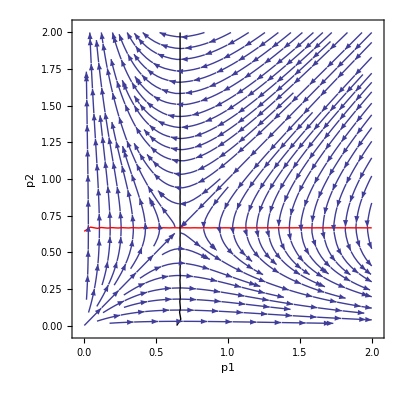

```mathematica
Show[StreamPlot[{p1(1-1.5p2),p2(1-1.5p1)},{p1,0,2},{p2,0,2}],
ContourPlot[
Evaluate[
Thread[egyenletek=={0,0}]],{p1,0,2},{p2,0,2},ContourStyle->{{Thick,Red},{Thick,Black}}],FrameLabel->{p1,p2}]
```

## predacio

```mathematica
egyenletek={p1(1-p2),p2(-1+p1)}
```

{p1 (1-p2),(-1+p1) p2}

```mathematica
Egyensúly=Solve[egyenletek=={0,0}]
```

{{p1→0,p2→0},{p1→1,p2→1}}

```mathematica
s=Solve[p1(1-1.5p2)==0]
```

{{p1→0.},{p2→0.666667}}

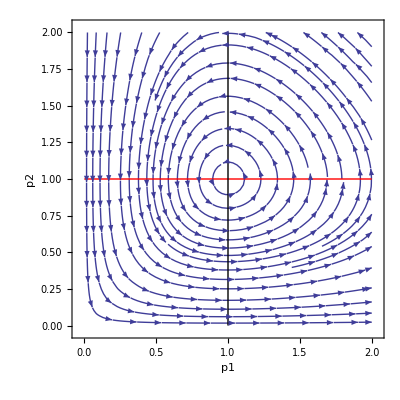

```mathematica
Show[StreamPlot[egyenletek,{p1,0,2},{p2,0,2}],
ContourPlot[
Evaluate[
Thread[egyenletek=={0,0}]],{p1,0,2},{p2,0,2},ContourStyle->{{Thick,Red},{Thick,Black}}],FrameLabel->{p1,p2}]
```

## mutualizmus

```mathematica
egyenletek={p1(1-1.5p1),p2(2-p1-p2)}
```

{(1-1.5 p1) p1,(2-p1-p2) p2}

```mathematica
Egyensúly=Solve[egyenletek=={0,0}]
```

{{p1→0.,p2→0.},{p1→0.,p2→2.},{p1→0.666667,p2→0.},{p1→0.666667,p2→1.33333}}

```mathematica
s=Solve[p1(1-1.5p2)==0]
```

{{p1→0.},{p2→0.666667}}

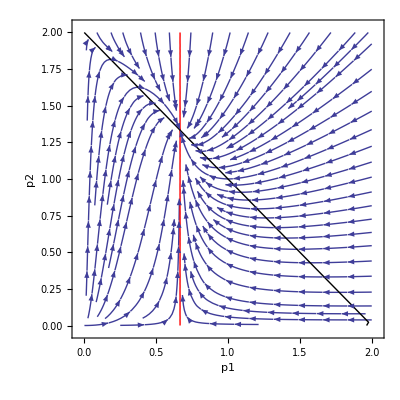

```mathematica
Show[StreamPlot[egyenletek,{p1,0,2},{p2,0,2}],
ContourPlot[
Evaluate[
Thread[egyenletek=={0,0}]],{p1,0,2},{p2,0,2},ContourStyle->{{Thick,Red},{Thick,Black}}],FrameLabel->{p1,p2}]
```